```mathematica
A*Integrate[Sin[wL *( t) + ϕ]^2 ⅇ^(-t/τ), {t, 0, ∞}, Assumptions->{wL ∈ Reals, τ>0}]
```

(A τ (1+4 wL^2 τ^2-Cos[2 ϕ]+2 wL τ Sin[2 ϕ]))/(2+8 wL^2 τ^2)

```mathematica
f[x_, τ_, ϕ_, A_, a_, b_, c_]:=A τ (1 + (2a (x-b)τ)^2 - Cos[2 ϕ] + 2 a (x-b) τ Sin[2ϕ])/(2(1+ (2 a (x-b) τ)^2))
```

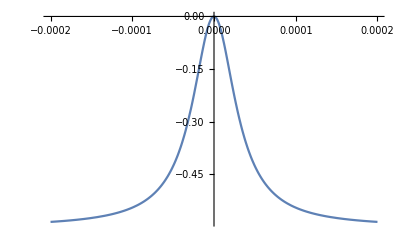

```mathematica
a := (1.4838* 9.27400968 10^-24)/(1.05457126 10^-34)
Plot[f[x, 120 10^-9, 0, -1*10^7, a, 0, 0], {x, -0.2*10^-3, 0.2*10^-3}]
```